## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="dPGM";
(*KeqEquilibrator=5.3;*)
KeqEquilibrator=0.7;

(* user will need to change this path *)
pathMASSFittingPackage = "C:/MASSef/";

mainFolder = "fit_dKd_PGM";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder];
```

C:\MASSef\data

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌(3pg)^c)^dPGM

Null;

Structure: 2

Active sites: 2

Km Values:

Substrate | Km_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
3pg | 0.0002 |  | M | 7 | 30 | trishcl | 0.03 | k | 0.02
cl | 0.02
mg2 | 0.005
so4 | 0.005
2pg | 0.00019 |  | M | 7 | 30 | trishcl | 0.03 | k | 0.02
cl | 0.02
mg2 | 0.005
so4 | 0.005

S0.5 Values:

Substrate | S0.5_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
3pg | Null | 330 | 1/s | 7 | 30 | trishcl | 0.03 | k | 0.02
cl | 0.02
mg2 | 0.005
so4 | 0.005
2pg | Null | 220 | 1/s | 7 | 30 | trishcl | 0.03 | k | 0.02
cl | 0.02
mg2 | 0.005
so4 | 0.005

Inhibition Values:

Parameter_Type | Inhibitor | Value | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Parameter_Type | Activator | Value | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Construct enzyme module

```mathematica
Overscript[(2pg)^c⇌(3pg)^c, dPGM]
```

```mathematica
"no reported mechanism"
```

```mathematica
catalyticBranch={"E_dPGM[c] + 2pg[c] <=> E_dPGM[c]&2pg",
				"E_dPGM[c]&2pg <=> E_dPGM[c]&3pg",
				"E_dPGM[c]&3pg<=> E_dPGM[c] + 3pg[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

### Setup King-Altmann Equations

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs];


(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getRateConstSubRandomMech[enzymeModel, eqRateConstSub, allCatalyticReactions, nonCatalyticReactions];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];


(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
pHandT={8.9, 22};

kmFittingData= simulateKmData[rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath,  fileList, KeqEquilibrator];

kcatFittingData=simulateKcatData[rxn, metsFull,  metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			  fileList, KeqEquilibrator];


haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];
```

{0.0539867,0.0539867}

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];
fittingData = Flatten[{kmFittingData,kcatFittingData, KeqFittingData}, 1];

dataPath =FileNameJoin[{inputPath,rxnName <>".dat"}, OperatingSystem->$OperatingSystem];

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath]
```

Keq_dPGM	2pg[c]	3pg[c]	param_E_total	param_pH	param_Temp	FileFlag	Target_Data
0.7	0	0.00002	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.09090909090909091
0.7	0	0.00003169786384922229	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.13680688860321008
0.7	0	0.00005023772863019165	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.2007600089131019
0.7	0	0.00007962143411069939	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.2847472489508013
0.7	0	0.0001261914688960386	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.38686317984685686
0.7	0	0.00020000000000000004	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.5
0.7	0	0.0003169786384922229	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.6131368201531432
0.7	0	0.0005023772863019165	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.7152527510491988
0.7	0	0.0007962143411069948	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.7992399910868982
0.7	0	0.0012619146889603862	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.8631931113967899
0.7	0	0.0020000000000000005	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateRev_3pg.txt	0.9090909090909091
0.7	0.000018999999999999994	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.09090909090909087
0.7	0.00003011297065676116	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.13680688860321003
0.7	0.00004772584219868205	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.20076000891310186
0.7	0.0000756403624051644	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.2847472489508012
0.7	0.00011988189545123664	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.38686317984685686
0.7	0.00018999999999999996	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.49999999999999994
0.7	0.0003011297065676116	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.6131368201531432
0.7	0.0004772584219868205	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.7152527510491987
0.7	0.0007564036240516448	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.7992399910868982
0.7	0.0011988189545123664	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.8631931113967899
0.7	0.0018999999999999996	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\relRateFor_2pg.txt	0.9090909090909092
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0	0.01	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateRev.txt	330
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0.01	0	1	7	30	C:\MASSef\examples\fit_dKd_PGM\input\absRateFor.txt	220
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7
0.7	0	0	1	8.9	22	C:\MASSef\examples\fit_dKd_PGM\input\haldaneRatio.txt	0.7

## Configure the Particle Swarm Optimization

```mathematica
numTrials=1;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[C:\\MASSef\\examples\\fit_dKd_PGM\\input\\absRateFor.txt,C:\\MASSef\\examples\\fit_dKd_PGM\\input\\absRateRev.txt,C:\\MASSef\\examples\\fit_dKd_PGM\\input\\relRateFor_2pg.txt,C:\\MASSef\\examples\\fit_dKd_PGM\\input\\relRateRev_3pg.txt,C:\\MASSef\\examples\\fit_dKd_PGM\\input\\haldaneRatio.txt]
data_file_name	C:\MASSef\examples\fit_dKd_PGM\input\dPGM.dat
value_row	-1
function_row	-2
data_row_high	-2
summary_file_name	C:\MASSef\examples\fit_dKd_PGM\output\raw\summary.txt
ultimate_result_name	C:\MASSef\examples\fit_dKd_PGM\output\raw\psoResults.txt

## Configure the Levenberg-Marquardt Algorithm

```mathematica
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, dataPath, finalRateConsts, fileList, lowerParamBound, upperParamBound];
```

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
candidates_import_path	C:\MASSef\examples\fit_dKd_PGM\output\raw\psoResults.txt
candidates_export_path	C:\MASSef\examples\fit_dKd_PGM\output\raw\lmaResults.txt
filesWithFunctions	[C:\\MASSef\\examples\\fit_dKd_PGM\\input\\absRateFor.txt,C:\\MASSef\\examples\\fit_dKd_PGM\\input\\absRateRev.txt,C:\\MASSef\\examples\\fit_dKd_PGM\\input\\relRateFor_2pg.txt,C:\\MASSef\\examples\\fit_dKd_PGM\\input\\relRateRev_3pg.txt,C:\\MASSef\\examples\\fit_dKd_PGM\\input\\haldaneRatio.txt]
data_file_name	C:\MASSef\examples\fit_dKd_PGM\input\dPGM.dat
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python",runFitScriptPath , psoParameterPath, lmaParameterPath, psoTrialSummaryFileName, psoResultsFileName, lmaResultsFileName, ToString @numTrials, dataPath}, " "];

runBothCmd="cd "<>inputPath<>" && "<>runPythonCmd
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"]
```

cd C:\MASSef\examples\fit_dKd_PGM\input && python C:\MASSef\python_code\src\run_fit_rel.py C:\MASSef\examples\fit_dKd_PGM\input\psoParameters.txt C:\MASSef\examples\fit_dKd_PGM\input\lmaParameters.txt C:\MASSef\examples\fit_dKd_PGM\output\raw\summary.txt C:\MASSef\examples\fit_dKd_PGM\output\raw\psoResults.txt C:\MASSef\examples\fit_dKd_PGM\output\raw\lmaResults.txt 1 C:\MASSef\examples\fit_dKd_PGM\input\dPGM.dat

best_fit: 0.797964768333
True

#### Run the PSO Algorithm Independently - not working

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh"

(*You can copy+paste this output to a shell*)
```

cd /home/mrama/Dropbox/Kinetics/Enzymes_new/GAPD_dKd/Parameter_Fitting/Development/ && ./runPso.sh

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runShRunPsoCmd="!"<>runShRunPsoExec<>" 2>&1";
Import[runShRunPsoCmd,"Text"]
```

#### Run the Levenberg-Marquardt Algorithm Independently - not working

The Levenberg-Marquardt Algorithm needs to be run after the Particle Swarm Optimization

```mathematica
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

python /media/users/jdebree/ProjectFiles/Scripts/lma_ver0.10.1.py /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaParameters.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/psoResults.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
lmaRunExe="!"<>lmaRunCmd<>" 2>&1";
Import[lmaRunExe,"Text"]
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
fittingData = Import[FileNameJoin[{inputPath, "dPGM.dat"}, OperatingSystem->$OperatingSystem]];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw","lmaResults.txt"}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,""];
```

```mathematica
ssdValue = Total[bestFitDetails[[#,3]]&/@Table[i,{i,3,Dimensions[bestFitDetails][[1]]}]]
```

7.79942×10^-7

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
relRateRev_3pg | 0.000296237 | 8.77566×10^-8 | 0.0682345 | 0.0909091 | 0.0909711
relRateRev_3pg | 0.000281276 | 7.91164×10^-8 | 0.0647872 | 0.136807 | 0.136896
relRateRev_3pg | 0.000260431 | 6.78241×10^-8 | 0.0599843 | 0.20076 | 0.20088
relRateRev_3pg | 0.000233056 | 5.43152×10^-8 | 0.0536776 | 0.284747 | 0.2849
relRateRev_3pg | 0.000199775 | 3.99102×10^-8 | 0.0460105 | 0.386863 | 0.387041
relRateRev_3pg | 0.000162906 | 2.65382×10^-8 | 0.0375174 | 0.5 | 0.500188
relRateRev_3pg | 0.000126039 | 1.58858×10^-8 | 0.0290258 | 0.613137 | 0.613315
relRateRev_3pg | 0.0000927663 | 8.6056×10^-9 | 0.0213625 | 0.715253 | 0.715406
relRateRev_3pg | 0.0000654025 | 4.27749×10^-9 | 0.0150606 | 0.79924 | 0.79936
relRateRev_3pg | 0.0000445671 | 1.98623×10^-9 | 0.0102625 | 0.863193 | 0.863282
relRateRev_3pg | 0.0000296147 | 8.77028×10^-10 | 0.00681926 | 0.909091 | 0.909153
relRateFor_2pg | 0.000296433 | 8.78724×10^-8 | 0.0682329 | 0.0909091 | 0.0908471
relRateFor_2pg | 0.000281471 | 7.92262×10^-8 | 0.0647902 | 0.136807 | 0.136718
relRateFor_2pg | 0.000260624 | 6.79248×10^-8 | 0.0599928 | 0.20076 | 0.20064
relRateFor_2pg | 0.000233244 | 5.44027×10^-8 | 0.0536919 | 0.284747 | 0.284594
relRateFor_2pg | 0.000199951 | 3.99806×10^-8 | 0.0460299 | 0.386863 | 0.386685
relRateFor_2pg | 0.000163063 | 2.65896×10^-8 | 0.0375396 | 0.5 | 0.499812
relRateFor_2pg | 0.000126172 | 1.59193×10^-8 | 0.0290479 | 0.613137 | 0.612959
relRateFor_2pg | 0.000092871 | 8.62503×10^-9 | 0.0213821 | 0.715253 | 0.7151
relRateFor_2pg | 0.0000654804 | 4.28769×10^-9 | 0.0150763 | 0.79924 | 0.799119
relRateFor_2pg | 0.0000446224 | 1.99116×10^-9 | 0.0102742 | 0.863193 | 0.863104
relRateFor_2pg | 0.0000296524 | 8.79264×10^-10 | 0.00682748 | 0.909091 | 0.909029
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateRev | 9.25704×10^-11 | 8.56928×10^-21 | 2.1315×10^-8 | 330 | 330.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
absRateFor | 2.19289×10^-10 | 4.80877×10^-20 | 5.04931×10^-8 | 220 | 220.
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035
haldaneRatio | 0.0000216396 | 4.68271×10^-10 | 0.00498282 | 0.7 | 0.700035

### Simulated Data and Best Fit Data Plot

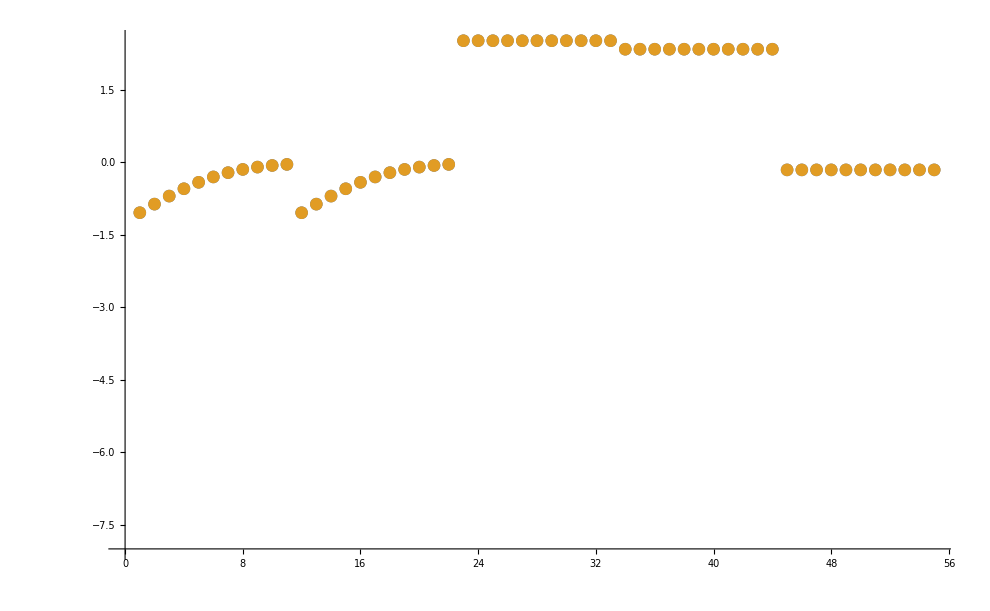

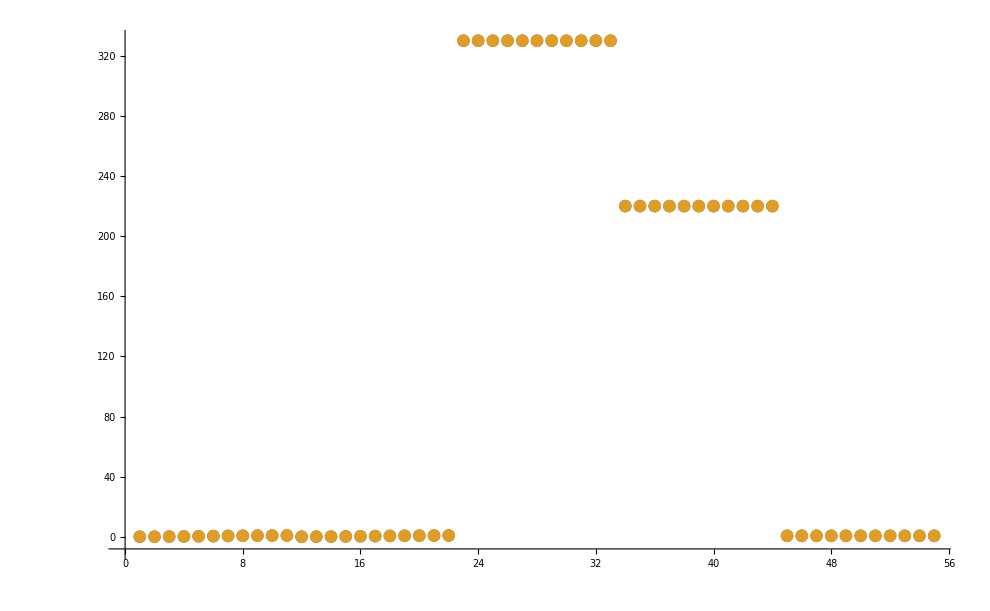

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

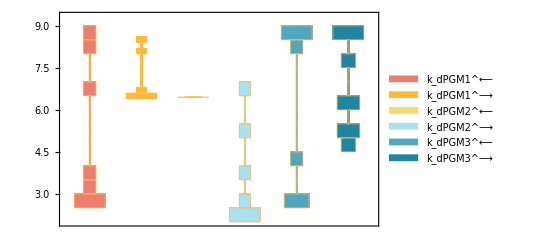

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

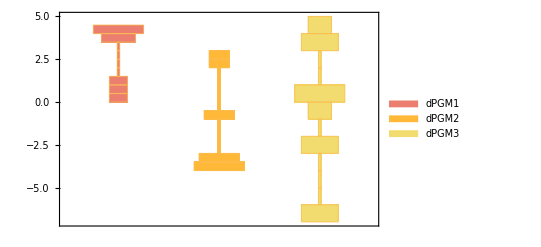

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

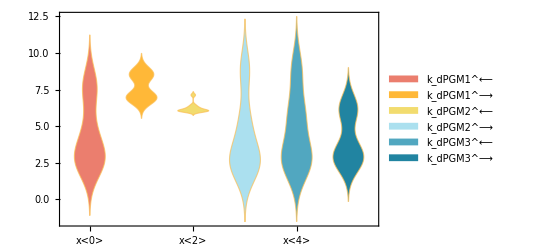

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[inputPath  <> "(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

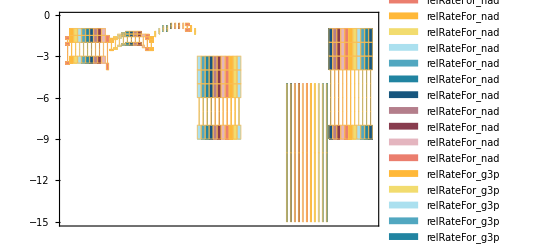

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= Underscript[E_total, Global]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.0002 | 0.00019985 | 0.0750067
0.00019 | 0.000190143 | 0.0751074

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
330 | 330. | 2.1315×10^-8
220 | 220. | 5.04931×10^-8

```mathematica
(*Backcalculated Haldane*)
(220/0.00019)/(330/0.0002)
```

0.701754

```mathematica
1/((330/0.0002)/(220/0.00019))
```

0.701754

```mathematica
((220+13)/(0.00019-0.000035))
((330-11)/(0.0002+0.000027))
((220+13)/(0.00019-0.000035))/((330-11)/(0.0002+0.000027))
```

1.50323×10^6

1.40529×10^6

1.06969

```mathematica
N@330/200
```

1.65

```mathematica
N@330/190
```

```mathematica
((330+11)/(0.0002-0.000027))/((220-13)/(0.00019+0.000035))
```

2.1425